```mathematica
Table[Arg[ⅈ^n],{n,0,15}]
```

{0,π/2,π,-π/2,0,π/2,π,-π/2,0,π/2,π,-π/2,0,π/2,π,-π/2}

```mathematica
Table[Abs[ⅈ^n],{n,0,15}] // Simplify
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

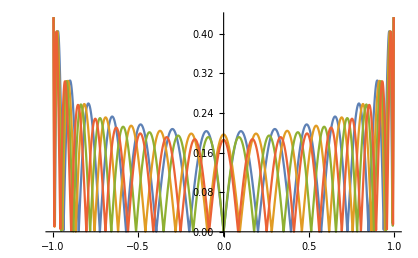

```mathematica
Plot[Evaluate@Table[Abs[LegendreP[n,w]],{n,15,18}],{w,-1,1},ImageSize->{418,258},AspectRatio->Full]
```

```mathematica
Export["/Users/tiao/Dropbox/UNSW/honours-thesis/figures/amplitude_response.pdf",%21,"PDF"]
```

/Users/tiao/Dropbox/UNSW/honours-thesis/figures/amplitude_response.pdf

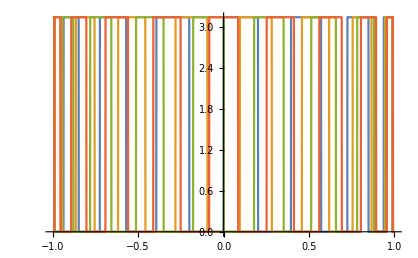

```mathematica
Plot[Evaluate@Table[Arg[LegendreP[n,w]],{n,15,18}],{w,-1,1},ImageSize->{418,258},AspectRatio->Full]
```

```mathematica
Simplify[Table[Arg[LegendreP[n,w]],{n,0,5}],w∈Reals]
```

{0,Arg[w],Arg[-1+3 w^2],Arg[-3 w+5 w^3],Arg[3-30 w^2+35 w^4],Arg[15 w-70 w^3+63 w^5]}

```mathematica
?N
```

N[expr] gives the numerical value of expr. 
N[expr,n] attempts to give a result with n-digit precision.

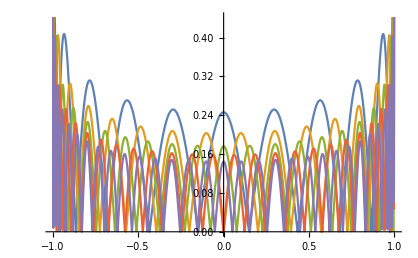

```mathematica
Plot[Evaluate@Table[Abs[LegendreP[n,w]],{n,10,30,5}],{w,-1,1},ImageSize->{418,258},AspectRatio->Full]
```

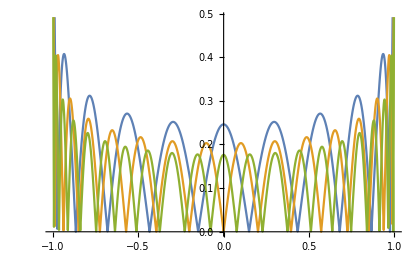

```mathematica
Plot[Evaluate@Table[Abs[LegendreP[n,w]],{n,10,20,5}],{w,-1,1},ImageSize->{418,258},AspectRatio->Full]
```

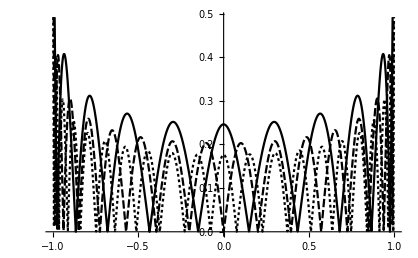

```mathematica
Plot[Evaluate[Table[Abs[LegendreP[n,w]],{n,10,20,5}]],{w,-1,1},PlotTheme->"Monochrome",ImageSize->{418,258},AspectRatio->Full]
```

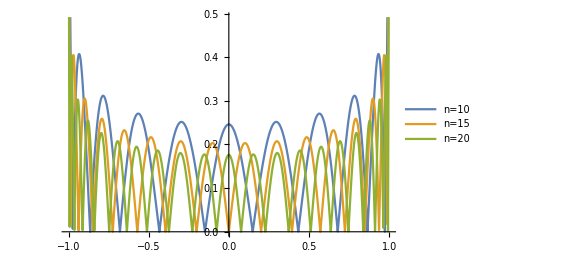

```mathematica
Plot[Evaluate[Table[Abs[LegendreP[n,w]],{n,10,20,5}]],{w,-1,1},PlotLegends-> Placed[{"n=10","n=15","n=20"},Above],PlotTheme->Automatic,ImageSize->{418,258},AspectRatio->Full]
```

```mathematica
Table[Abs[LegendreP[n,w]],{n,10,20,5}]
```

{1/256 Abs[-63+3465 w^2-30030 w^4+90090 w^6-109395 w^8+46189 w^10],Abs[-6435 w+255255 w^3-2909907 w^5+14549535 w^7-37182145 w^9+50702925 w^11-35102025 w^13+9694845 w^15]/2048,1/262144 Abs[46189-9699690 w^2+334639305 w^4-4461857400 w^6+30117537450 w^8-116454478140 w^10+273491577450 w^12-396713057400 w^14+347123925225 w^16-167890003050 w^18+34461632205 w^20]}

```mathematica
Plot[Evaluate[Table[Abs[LegendreP[n,w]],{n,10,20,5}]],{w,-1,1},PlotLegends-> Placed[{"n=10","n=15","n=20"},Above],PlotTheme->Automatic,ImageSize->{418,258},AspectRatio->Full]
```

-Graphics-

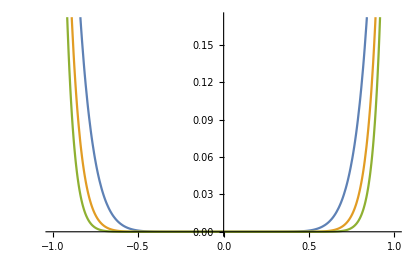

```mathematica
Plot[Evaluate[Table[Abs[w^n],{n,10,20,5}]],{w,-1,1},PlotTheme->Automatic,ImageSize->{418,258},AspectRatio->Full]
```

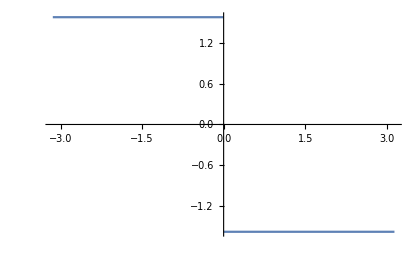

```mathematica
Plot[Arg[(ⅈ ω/π)^3],{ω,-π,π},ImageSize->{418,258},AspectRatio->Full]
```